```mathematica
Off[RowReduce::luc]
Off[Solve::svars]
$Assumptions={θ>0,n∈Integers,m∈Integers,j∈Integers,i∈Integers,n≥0,m≥0,j≥0,i≥0};
SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];
```

## Some Testing with Hermite Functions (non-normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(v)f0[c];
H[i_,c_]=1/(i!2^(i/2))HermiteH[i,c/√2];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/(2n!),OddQ[m-n],1/(√(2 π))1/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

```mathematica
Table[k!∫_(-∞)^∞ H[k,c]^2 f0[c]ⅆc,{k,0,4}]
Table[Expand[(i+1)H[i+1,c]-(c H[i,c]- H[i-1,c])],{i,1,10}]
FullSimplify[D[H[i,c],c]-H[i-1,c]]
FullSimplify[D[H[i,c]f0[c],c]+(i+1)H[i+1,c]f0[c]]
Table[(∫_(-∞)^∞ (c)^n fG[c,10]ⅆc),{n,0,4}]
Table[n!(∫_(-∞)^∞ H[n,c](fM[c]-fG[c,5])ⅆc),{n,0,4}]/.{α[0]->v}
```

{1,1,1,1,1}

{0,0,0,0,0,0,0,0,0,0}

0

0

{α[0],α[1],α[0]+α[2],3 α[1]+α[3],3 α[0]+6 α[2]+α[4]}

{0,-α[1],-α[2],-α[3],-α[4]}

```mathematica
∫_(-∞)^∞ H[1,c]fG[c,5]ⅆc
```

α[1]

```mathematica
Expand[H[1,c]]
```

c

```mathematica
Table[HSpcInt[n,m],{n,0,3},{m,0,5}]
Table[∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc,{n,0,3},{m,0,5}]
```

{{1/2,1/(√(2 π)),0,-1/(6 √(2 π)),0,1/(40 √(2 π))},{1/(√(2 π)),1/2,1/(2 √(2 π)),0,-1/(24 √(2 π)),0},{0,1/(2 √(2 π)),1/4,1/(4 √(2 π)),0,-1/(48 √(2 π))},{-1/(6 √(2 π)),0,1/(4 √(2 π)),1/12,1/(16 √(2 π)),0}}

{{1/2,1/(√(2 π)),0,-1/(6 √(2 π)),0,1/(40 √(2 π))},{1/(√(2 π)),1/2,1/(2 √(2 π)),0,-1/(24 √(2 π)),0},{0,1/(2 √(2 π)),1/4,1/(4 √(2 π)),0,-1/(48 √(2 π))},{-1/(6 √(2 π)),0,1/(4 √(2 π)),1/12,1/(16 √(2 π)),0}}

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

```mathematica
Table[∫_(-∞)^∞ H[k,c]^2 f0[c]ⅆc,{k,0,4}]
Table[Expand[√(i+1)H[i+1,c]-(c H[i,c]- √i H[i-1,c])],{i,1,10}]
FullSimplify[D[H[i,c],c]-√i H[i-1,c]]
FullSimplify[D[H[i,c]f0[c],c]+√(i+1)H[i+1,c]f0[c]]
Table[(∫_(-∞)^∞ (c)^n fG[c,4]ⅆc),{n,0,4}]
Table[(∫_(-∞)^∞ H[n,c](fM[c]-fG[c,5])ⅆc),{n,0,4}]/.{α[0]->ρ,α[1]->v,α[2]->θ/√2}
```

{1,1,1,1,1}

{0,0,0,0,0,0,0,0,0,0}

0

0

{α[0],α[1],α[0]+√2 α[2],3 α[1]+√6 α[3],3 (α[0]+2 √2 α[2])}

{0,0,0,-α[3],-α[4]}

```mathematica
∫_(-∞)^∞ (c)^2 fM[c]ⅆc
```

θ+ρ

```mathematica
Expand[H[2,c]]
```

-1/(√2)+c^2/(√2)

```mathematica
Expand[√6 H[3,c]]
```

-3 c+c^3

```mathematica
Table[HSpcInt[n,m],{n,0,3},{m,0,5}]
Table[∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc,{n,0,3},{m,0,5}]
```

{{1/2,1/(√(2 π)),0,-1/(2 √(3 π)),0,1/4 √(3/(5 π))},{1/(√(2 π)),1/2,1/(2 √π),0,-1/(4 √(3 π)),0},{0,1/(2 √π),1/2,1/2 √(3/(2 π)),0,-1/4 √(5/(6 π))},{-1/(2 √(3 π)),0,1/2 √(3/(2 π)),1/2,3/(4 √(2 π)),0}}

{{1/2,1/(√(2 π)),0,-1/(2 √(3 π)),0,1/4 √(3/(5 π))},{1/(√(2 π)),1/2,1/(2 √π),0,-1/(4 √(3 π)),0},{0,1/(2 √π),1/2,1/2 √(3/(2 π)),0,-1/4 √(5/(6 π))},{-1/(2 √(3 π)),0,1/2 √(3/(2 π)),1/2,3/(4 √(2 π)),0}}

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

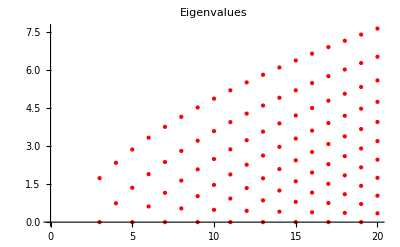

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Pre-Computing Boundary Conditions

```mathematica
Clear[nn,kn,sol1,sol2,solBC,ev,ew,solW,bc]
NN=30;

rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((NN-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧]

bc[k_]:=Collect[Expand[β1 α[k]+√(π/2)((rhoW HSpcInt[k,0]+0 HSpcInt[k,1]+θW/√2 HSpcInt[k,2])-∑_(j=0)^((NN-1)/2) α[2j]HSpcInt[k,2j])],β1,Simplify];

bc0=Table[bc[k],{k,3,NN,2}];
```

-θW/2+α[0]+α[2]/(√2)-α[4]/(2 √6)+α[6]/(4 √5)-1/8 √(5/14) α[8]+1/48 √7 α[10]-1/32 √(21/11) α[12]+1/32 √(33/26) α[14]-1/128 √(143/10) α[16]+1/256 √(715/17) α[18]-1/512 √(2431/19) α[20]+1/512 √(4199/42) α[22]-(√(29393/23) α[24])/2048+(√(52003/2) α[26])/10240-(5 √(7429/6) α[28])/12288

## Solving

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

GetSolution[nvar_,kn_,thetaw_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];

bcEqn=Table[bc0⟦i⟧/.Table[α[k]->0,{k,nvar,NN}],{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};
solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)
{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn}
]
```

```mathematica
(*u[x_]=GetSolution[4,0.1,1.0]
Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]]/.{Kn->0.1}]]
*)
```

```mathematica
GetSolution[5,0.1,1.0]
```

{1.45349 x,-0.436048}

## Numerical Reference

```mathematica
While[!($Context=="Global`"),End[]]
Print["Old Context is: ",$Context]
Begin["numerical2`"];
$ContextPath=Delete[$ContextPath,Position[$ContextPath,"Global`"]];
$ContextPath=Append[$ContextPath,"numerical2`"]
Print["New Context is: ",$Context]
```

Old Context is: Global`

{DocumentationSearch`,ResourceLocator`,PacletManager`,QuantityUnits`,WebServices`,System`,numerical2`}

New Context is: numerical2`

In this context no variables from the global context is visible, expect when addressed directly via: Global`varname
Any new symbol will be created in the new context, irrespectively of the existence of the symbol name in the Global` context.
When ending the context the Global` variables will become solely visible again. 
Variables from the new context can then be addressed by, e.g., Numerical`varname

```mathematica
Zahl[α_]:=If[StringLength[ToString[α]]<3 || α≥10,StringJoin[ToString[α],"0"],ToString[α]];
Filename[type_,tau_,nst_,Nc_,cMax_]:=StringJoin["Result_",type,
"_tau",StringReplace[Zahl[tau],"."->"p"],
"_nst",ToString[nst],
"_Nc",ToString[Nc],
"_cMax",StringReplace[Zahl[cMax],"."->"p"],
".dat"];

Filename["Kinetic",0.1,50,30,20,5.0]

Load[type_,tau_,nst_,Nc_,cMax_]:=Block[{fp},
fp=Filename[type,tau, nst,Nc,cMax];
ReadList[fp,Number,RecordLists->True]
];

GetData[uT_,Neq_]:=Table[Interpolation[uT⟦All,{1,i}⟧,InterpolationOrder->1],{i,2,1+Neq}];

SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference"]
```

Filename[Kinetic,0.1,50,30,20,5.]

SetDirectory::cdir: Cannot set current directory to "/home/torrilhon/Documents/RWTH/Projects/KineticReference".

$Failed

C:\Users\mt\Science\Projekte\KineticReference

```mathematica
nr=1;
Type="BGK1DSimpleHeat";
τ=0.1;
nst=300;
Nc=150;
cMax=5.0;

xa=-0.5;
xe=0.5;

{ρ[nr],vx[nr],θ[nr],p[nr],qx[nr]}=GetData[Load[Type,τ,nst,Nc,cMax],5];
```

```mathematica
nr=2;
Type="BGK1DSimpleHeat";
τ=0.1;
nst=200;
Nc=100;
cMax=5.0;

xa=-0.5;
xe=0.5;

{ρ[nr],vx[nr],θ[nr],p[nr],qx[nr]}=GetData[Load[Type,τ,nst,Nc,cMax],5];
```

```mathematica
θ[1][-0.5]
```

0.791798

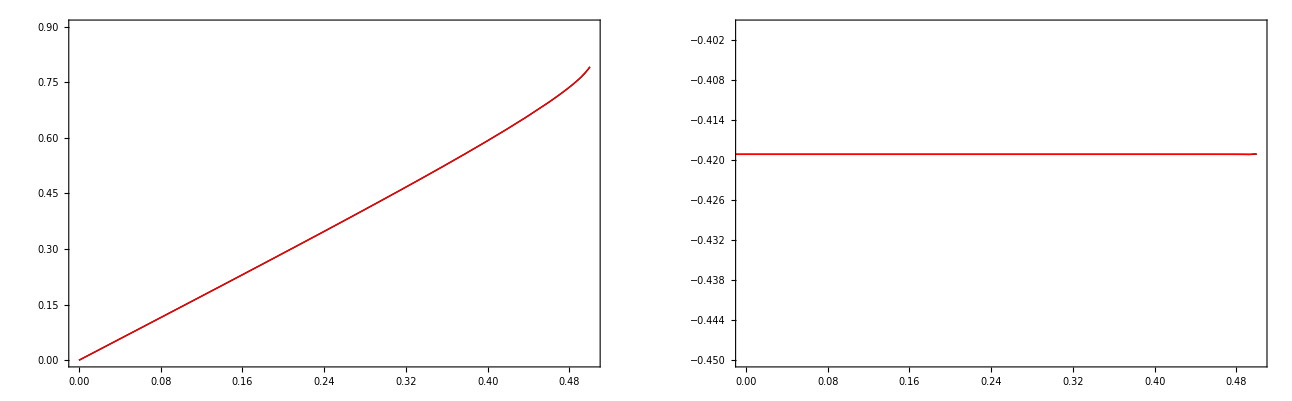

```mathematica
SetOptions[Plot,PlotStyle->{{Black,Thick},{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},BaseStyle->{Medium,FontFamily->"Helvetica"},Frame->True,ImageSize->600];
GraphicsGrid[{
{Plot[{θ[1][-x],θ[2][-x]},{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.9}}],
Plot[{-qx[1][x],-qx[2][x]},{x,xa,xe},PlotRange->{{0,1/2},{-0.45,-0.4}}]}}]
```

```mathematica
θX[x_]=θ[1][-x];
qX[x_]=-qx[1][x];
```

```mathematica
Print["Old Context is: ",$Context]
End[];
$ContextPath=Delete[$ContextPath,Position[$ContextPath,"numerical2`"]];
$ContextPath=Append[$ContextPath,"Global`"]
Print["New Context is: ",$Context]
```

Old Context is: numerical2`

{DocumentationSearch`,ResourceLocator`,PacletManager`,QuantityUnits`,WebServices`,System`,Global`}

New Context is: Global`

## Solution Plots (Kn=0.1)

```mathematica
ix=3;
Solution[ix]=Table[GetSolution[n,0.1,1.0],{n,5,NN}];
```

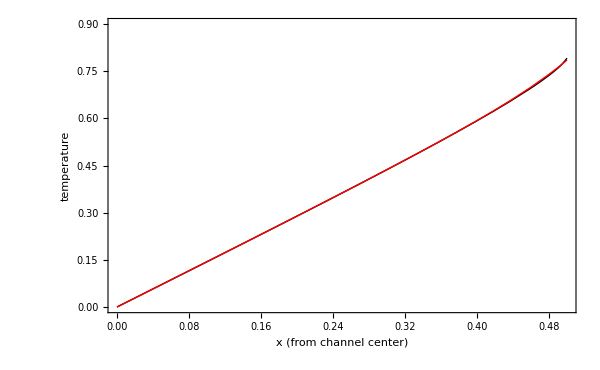

```mathematica
Plot[Evaluate[{numerical2`θX[x],Solution[ix]⟦20,1⟧}],{x,-0.5,0.5},Frame->True,PlotRange->{{0,0.5},{0,0.9}},PlotStyle->{{Thick,Black},Red,Blue,Green,Purple,Cyan},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"x (from channel center)","temperature","1D Kinetic Equation: Kn = 0.1 (G5-Red, G6-Blue, G7-Green, G8-Purple, G9-Cyan, exact-Black)"}]
```

```mathematica
θNSF[x_]=1.4534944552264861 x;
```

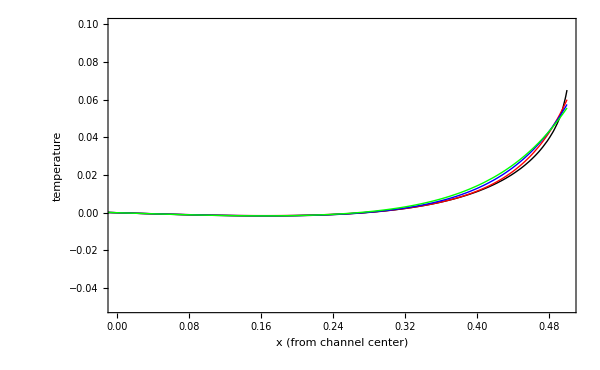

```mathematica
Plot[Evaluate[{numerical2`θX[x]-θNSF[x],Solution[ix]⟦26,1⟧-θNSF[x],Solution[ix]⟦14,1⟧-θNSF[x],Solution[ix]⟦10,1⟧-θNSF[x]}],{x,-0.5,0.5},Frame->True,PlotRange->{{0,0.5},{-0.05,0.1}},PlotStyle->{{Thick,Black},Red,Blue,Green,Purple,Cyan},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"x (from channel center)","temperature","1D Kinetic Equation: Kn = 0.1 (G5-Red, G6-Blue, G7-Green, G8-Purple, G9-Cyan, exact-Black)"}]
```

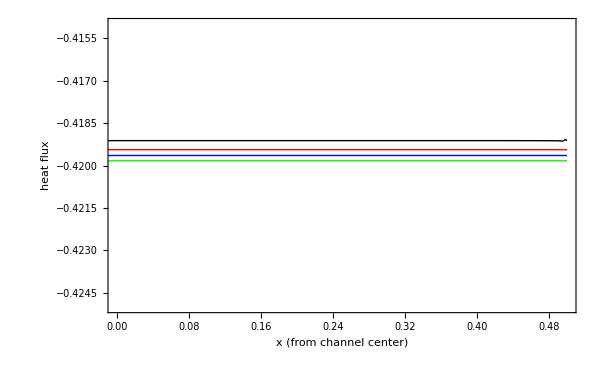

```mathematica
Plot[Evaluate[{numerical2`qX[x],Solution[ix]⟦26,2⟧,Solution[ix]⟦14,2⟧,Solution[ix]⟦10,2⟧}],{x,-0.5,0.5},Frame->True,PlotRange->{{0,0.5},{-0.425,-0.415}},PlotStyle->{{Thick,Black},Red,Blue,Green,Purple,Cyan},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"x (from channel center)","heat flux","1D Kinetic Equation: Kn = 0.1 (G5-Red, G6-Blue, G7-Green, G8-Purple, G9-Cyan, exact-Black)"}]
```

## Solution Convergence

```mathematica
Solution[1]=Table[GetSolution[n,0.1,1.0],{n,5,NN}];
```

```mathematica
Solution[2]=Table[GetSolution[n,0.05,1.0],{n,5,NN}];
```

```mathematica
Do[
TempW[k]=Table[{4+i,1-Solution[k]⟦i,1⟧/.{x->0.5}},{i,1,Length[Solution[k]]}];
,{k,1,3}]
```

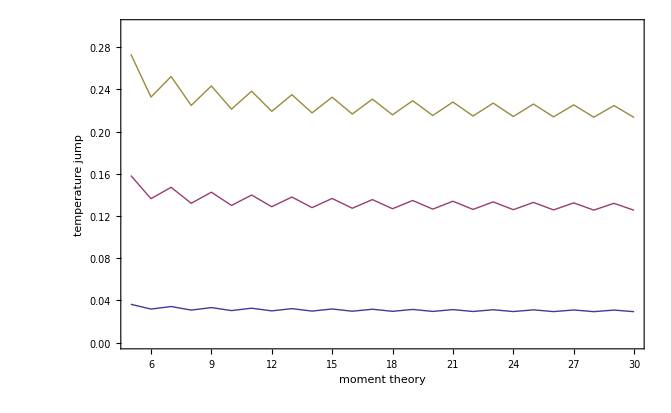

```mathematica
ListPlot[{TempW[1],TempW[2],TempW[3]},Joined->True,Frame->True,PlotRange->{All,{0.0,0.3}},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"moment theory","temperature jump","1D Kinetic Equation: Kn = 0.1, 0.05, 0.01"}]
```

```mathematica
Do[
HeatFlux[k]=Table[{4+i,Solution[k]⟦i,2⟧/.{x->0.5}},{i,1,Length[Solution[k]]}];
,{k,1,3}]
```

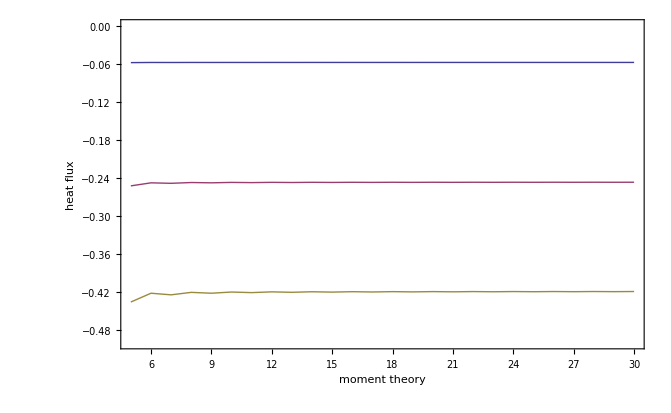

```mathematica
ListPlot[{HeatFlux[1],HeatFlux[2],HeatFlux[3]},Joined->True,Frame->True,PlotRange->{All,{-0.5,0.0}},BaseStyle->{Medium,FontFamily->"Helvetia"},FrameLabel->{"moment theory","heat flux","1D Kinetic Equation: Kn = 0.1, 0.05, 0.01"}]
```